# Triatomic Reaction with LEPS Potential

```mathematica
rAB=.;rBC=.;rAC=.;
Clear[rAB,rBC,rAC,a,b,c,dAB,dBC,dAC,rMin,rMax,q,j];
```

```mathematica
q[r_]=(d/2)((3/2)*e^(−2α(r−r0))−e^(−α(r−r0)))
(*remember functions use [], not ()*)
```

1/2 d (3/2 e^(-2 (r-r0) α)-e^(-((r-r0) α)))

```mathematica
j[r_]=(d/4)(e^(−2α(r−r0))−6e^(−α(r−r0)))
```

1/4 d (e^(-2 (r-r0) α)-6 e^(-((r-r0) α)))

```mathematica
a=.05;b=0.3;c=0.05;dAB=4.746;dBC=4.746;dAC=3.445;r0Sub=0.742;αSub=1.942;

qAB=q[rAB]/.{d->dAB,r0->r0Sub,α->αSub}
qBC=q[rBC]/.{d->dBC,r0->r0Sub,α->αSub}
qAC=q[rAC]/.{d->dAC,r0->r0Sub,α->αSub}

jAB=j[rAB]/.{d->dAB,r0->r0Sub,α->αSub}
jBC=j[rBC]/.{d->dBC,r0->r0Sub,α->αSub}
jAC=j[rAC]/.{d->dAC,r0->r0Sub,α->αSub}
```

2.373 (3/2 e^(-3.884 (-0.742+rAB))-e^(-1.942 (-0.742+rAB)))

2.373 (3/2 e^(-3.884 (-0.742+rBC))-e^(-1.942 (-0.742+rBC)))

1.7225 (3/2 e^(-3.884 (-0.742+rAC))-e^(-1.942 (-0.742+rAC)))

1.1865 (e^(-3.884 (-0.742+rAB))-6 e^(-1.942 (-0.742+rAB)))

1.1865 (e^(-3.884 (-0.742+rBC))-6 e^(-1.942 (-0.742+rBC)))

0.86125 (e^(-3.884 (-0.742+rAC))-6 e^(-1.942 (-0.742+rAC)))

```mathematica
(*test to see if my notation is correct:

Vleps[rAB_,rBC_]:= (qab/(1+A))+(qbc/(1+B))+(qac/(1+C))-((jab^2)/((1+A)^2)+(jbc^2)/((1+B)^2)+(jac^2)/((1+C)^2)-(jab*jbc)/((1+A)(1+B))-(jbc*jac)/((1+B)(1+C))-(jab*jac)/((1+A)(1+C)))^(1/2);
Vleps[rAB,rBC];
*)
```

```mathematica
Vleps[rAB_,rBC_]:= (qAB/(1+a))+(qBC/(1+b))+(qAC/(1+c))-((jAB^2)/((1+a)^2)+(jBC^2)/((1+b)^2)+(jAC^2)/((1+c)^2)-(jAB*jBC)/((1+a)(1+b))-(jBC*jAC)/((1+b)(1+c))-(jAB*jAC)/((1+a)(1+c)))^(1/2)
Vleps[rAB,rBC]
```

2.26 (3/2 e^(-3.884 (-0.742+rAB))-e^(-1.942 (-0.742+rAB)))+1.64048 (3/2 e^(-3.884 (-0.742+rAC))-e^(-1.942 (-0.742+rAC)))+1.82538 (3/2 e^(-3.884 (-0.742+rBC))-e^(-1.942 (-0.742+rBC)))-√(1.2769 (e^(-3.884 (-0.742+rAB))-6 e^(-1.942 (-0.742+rAB)))^2-0.926869 (e^(-3.884 (-0.742+rAB))-6 e^(-1.942 (-0.742+rAB))) (e^(-3.884 (-0.742+rAC))-6 e^(-1.942 (-0.742+rAC)))+0.672791 (e^(-3.884 (-0.742+rAC))-6 e^(-1.942 (-0.742+rAC)))^2-1.03134 (e^(-3.884 (-0.742+rAB))-6 e^(-1.942 (-0.742+rAB))) (e^(-3.884 (-0.742+rBC))-6 e^(-1.942 (-0.742+rBC)))-0.748625 (e^(-3.884 (-0.742+rAC))-6 e^(-1.942 (-0.742+rAC))) (e^(-3.884 (-0.742+rBC))-6 e^(-1.942 (-0.742+rBC)))+0.833007 (e^(-3.884 (-0.742+rBC))-6 e^(-1.942 (-0.742+rBC)))^2)

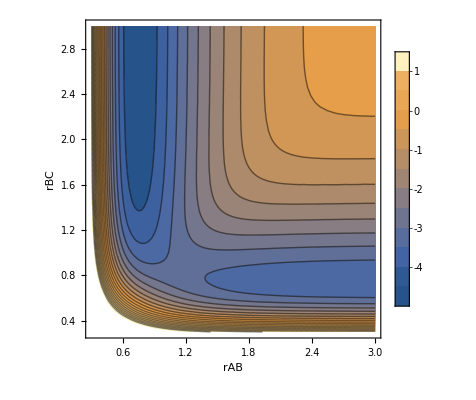

```mathematica
rMin=0.3;
rMax=3.0;
ContourPlot[Vleps[rAB,rBC],{rAB,rMin,rMax},{rBC,rMin,rMax},Contours->20,PlotLegends->{-4.5,-4,-3.5,-3,-2.5,-2,-1.5,-1,-.5,0,.5,1.0},FrameLabel->{"rAB","rBC"}]
```

## My Plot above was working a couple hours ago. Even now when I changed the legend scale it gave the output above. But after I went back and made additional variable subs r0 and alpha, it’s not giving output. Even before going that when I cleared variables and reran code, it wasn’t showing anymore. Don’t know what’s wrong and there’s no time so I’ll copy the given LEPS.

```mathematica
(*In lecture notes, we did chain rule instead of substituting expressions in terms of x in for the r variables*)
Grad
```